First we define 1D cubic Hermite Basis functions.  We also demonstrate some of their properties, e.g. where they are 1,0, where their derivatives are 1,0.

```mathematica
Subscript[ψ, 01][ξ_]:=1-3 ξ^2+2 ξ^3;
```

```mathematica
Subscript[ψ, 01][0]
```

1

```mathematica
Subscript[ψ, 01][1]
```

0

```mathematica
Dt[Subscript[ψ, 01][ξ],ξ]
```

-6 ξ+6 ξ^2

```mathematica
Subscript[ψ, 02][ξ_]:=ξ^2(3-2ξ);
```

```mathematica
Subscript[ψ, 02][0]
```

0

```mathematica
Subscript[ψ, 02][1]
```

1

```mathematica
Subscript[ψ, 11][ξ_]:=ξ(ξ-1)^2
```

```mathematica
Subscript[ψ, 11][0]
```

0

```mathematica
Subscript[ψ, 11][1]
```

0

```mathematica
Subscript[dψ, 11][ξ_]:=Dt[Subscript[ψ, 11][x],x]/.x->ξ
```

```mathematica
Subscript[dψ, 11][0]
```

1

```mathematica
Subscript[ψ, 12][ξ_]:=ξ^2(ξ-1)
```

```mathematica
Subscript[ψ, 12][0]
```

0

```mathematica
Subscript[dψ, 12][ξ_]:=Dt[Subscript[ψ, 12][x],x]/.x->ξ
```

```mathematica
Subscript[dψ, 12][1]
```

1

```mathematica
cubicHermite[ξ_]:={Subscript[ψ, 01][ξ],Subscript[ψ, 02][ξ],Subscript[ψ, 11][ξ],Subscript[ψ, 12][ξ]}
```

Now we define the 2D cubic hermit basis functions, but using the tensor product of the 1D basis functions.  We demonstrate the properties by graphically displaying the basis functions.

```mathematica
BiCubicHermite[x_, y_]:=KroneckerProduct[cubicHermite[x],cubicHermite[y]]
```

```mathematica
cubicHermite[0]
```

{1,0,0,0}

```mathematica
BiCubicHermite[x,y][[1]][[1]]
```

(1-3 x^2+2 x^3) (1-3 y^2+2 y^3)

```mathematica
GraphicsGrid[Table[
Plot3D[BiCubicHermite[x,y][[n]][[m]],{x,0,1},{y,0,1},AxesLabel->{Subscript[ξ, 1],Subscript[ξ, 2]}],
{n,1,4},{m,1,4}
]]
```

-Graphics-

```mathematica
MatrixForm[BiCubicHermite[Subscript[ξ, 1],Subscript[ξ, 2]]]
```

((1-3 ξ_1^2+2 ξ_1^3) (1-3 ξ_2^2+2 ξ_2^3) | (1-3 ξ_1^2+2 ξ_1^3) (3-2 ξ_2) ξ_2^2 | (1-3 ξ_1^2+2 ξ_1^3) (-1+ξ_2)^2 ξ_2 | (1-3 ξ_1^2+2 ξ_1^3) (-1+ξ_2) ξ_2^2
(3-2 ξ_1) ξ_1^2 (1-3 ξ_2^2+2 ξ_2^3) | (3-2 ξ_1) ξ_1^2 (3-2 ξ_2) ξ_2^2 | (3-2 ξ_1) ξ_1^2 (-1+ξ_2)^2 ξ_2 | (3-2 ξ_1) ξ_1^2 (-1+ξ_2) ξ_2^2
(-1+ξ_1)^2 ξ_1 (1-3 ξ_2^2+2 ξ_2^3) | (-1+ξ_1)^2 ξ_1 (3-2 ξ_2) ξ_2^2 | (-1+ξ_1)^2 ξ_1 (-1+ξ_2)^2 ξ_2 | (-1+ξ_1)^2 ξ_1 (-1+ξ_2) ξ_2^2
(-1+ξ_1) ξ_1^2 (1-3 ξ_2^2+2 ξ_2^3) | (-1+ξ_1) ξ_1^2 (3-2 ξ_2) ξ_2^2 | (-1+ξ_1) ξ_1^2 (-1+ξ_2)^2 ξ_2 | (-1+ξ_1) ξ_1^2 (-1+ξ_2) ξ_2^2)

Now, we flatten the 16 basis functions so that referring to them is easier.

```mathematica
bch[x_,y_]:=Flatten[BiCubicHermite[x,y]]
```

```mathematica
bch[Subscript[ξ, 1],Subscript[ξ, 2]].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

(1-3 ξ_1^2+2 ξ_1^3) (1-3 ξ_2^2+2 ξ_2^3)

Now we are going to define a  set of 1D linear Lagrange basis functions.

```mathematica
Subscript[φ, 1][ξ_]:=1-ξ
```

```mathematica
Subscript[φ, 2][ξ_]:=ξ
```

```mathematica
linearLagrange[ξ_]:={Subscript[φ, 1][ξ],Subscript[φ, 2][ξ]}
```

Now we define a set of 2D basis functions, based on 1D linear lagrange basis fucntions. Again, this is done by taking the tensor product of the 1D basis function sets.  And again, the properties are demonstrated by a graphical display.

```mathematica
BiLinearLagrange[x_,y_]:=KroneckerProduct[linearLagrange[x],linearLagrange[y]]
```

```mathematica
bll[x_,y_]:=Flatten[BiLinearLagrange[x,y]]
```

```mathematica
bll[x,y]
```

{(1-x) (1-y),(1-x) y,x (1-y),x y}

```mathematica
GraphicsGrid[Table[Plot3D[BiLinearLagrange[x,y][[n]][[m]],{x,0,1},{y,0,1}],{n,1,2},{m,1,2}]]
```

-Graphics-

Now we are going to try and use some of the 2D basis functions to do the "tri-quad" example.  This will consist of 3 elements, each element using BiCubicHermite basis functions.  The geometry is essentially determined by having the x,y,z coordinates each interpolated independently using the BiCubicHermite interpolation.  The aim is to have "C1" continuity, that is the x,y,z coordinates are continuous between elements, and their first derivatives are continuous.  The mixed second cross derivative is set to 0, though it could also just be set such that it is continuous between elements where they meet, however, initially, it is thought that it is simplest to set it to 0.

Firstly, α's are set for reuse for some y coordinates.

```mathematica
Subscript[α, 1]=√(1/3);Subscript[α, 2]=Subscript[α, 1]-√(3/4);Subscript[α, 3]=Subscript[α, 1]-√3;
```

Now, coordinate arrays are created for 7 global nodes.

```mathematica
X={-1,0,1,-.5,0,.5,0};
Y={Subscript[α, 1],Subscript[α, 1],Subscript[α, 1],Subscript[α, 2],0,Subscript[α, 2],Subscript[α, 3]};
(*Z={z1,z2,z3,0,0,0,0};*) (* This line is used when trying to symbolically satisfy C1 continuity constraint *)
Z={0.1,Subscript[α, 1],0.1,Subscript[α, 2],0,Subscript[α, 2],0.1};
```

Next, v___ values are set, these are x, and y components of tangent vectors at various node positions.
Firstly, some directions that are useful are set-up. Note that these will be relative to a plane, and there will be more than one plane.

```mathematica
ax=Cos[2π/12];
ay=Sin[2π/12];
bx=Cos[2π/6];
by=Sin[2π/6];
cx=Cos[2π/3];
cy=Sin[2π/3];
dx=Cos[2π 5/12];
dy=Sin[2π 5/12];
```

Now, define some planes.  One plane is the tanget plane at nodes 2,4,6 and 5, the other 3 planes are tangent planes at nodes 1,3 and 7.  The hypothesis is that if the tangent planes at 2,4,6 and 5 are parallel, then the edges 2-5, 4-5 and 6-5 will be C1 continuous, but that is just a guess.  If we are not that lucky, then a more restrictive requirement might be that points 2,4,6 and 5 have to be co-planar, and that that is the same plane as the tangent plane.

Plane 1 for nodes 2,4,6 and 5 tangent plane:

```mathematica
p1=Transpose[{
{1,0,1},
{0,1,1},
{0,0,0}
}] √(1/2);
```

```mathematica
ddx1Node2=p1.Transpose[{{0,1,0}}];
```

```mathematica
ddx1Node4=p1.Transpose[{{ax,ay,0}}];
```

```mathematica
ddx1Node6=p1.Transpose[{{bx,by,0}}];
```

```mathematica
ddx1Node5=p1.Transpose[{{0,1,0}}];
```

Now, set the arrays with tangent directions in the ξ_1 direction, for each of x, y and z.  Then do the same for ξ_2.

```mathematica
dXdx1={1,ddx1Node2[[1]][[1]],bx,ddx1Node4[[1]][[1]],ddx1Node5[[1]][[1]],ddx1Node6[[1]][[1]],bx};
dYdx1={0,ddx1Node2[[2]][[1]],by,ddx1Node4[[2]][[1]],ddx1Node5[[2]][[1]],ddx1Node6[[2]][[1]],by};
dZdx1={0,ddx1Node2[[3]][[1]],0,ddx1Node4[[3]][[1]],ddx1Node5[[3]][[1]],ddx1Node6[[3]][[1]],0};
```

Ok, now for the ξ_2 direction:

```mathematica
ddx2Node2=p1.Transpose[{{1,0,0}}];
```

```mathematica
ddx2Node4=p1.Transpose[{{cx,cy,0}}];
```

```mathematica
ddx2Node6=p1.Transpose[{{dx,dy,0}}];
```

```mathematica
ddx2Node5=p1.Transpose[{{-dx,-dy,0}}];
```

```mathematica
dXdx2={cx,ddx2Node2[[1]][[1]],-1,ddx2Node4[[1]][[1]],ddx2Node5[[1]][[1]],ddx2Node6[[1]][[1]],cx};
dYdx2={cy,ddx2Node2[[2]][[1]],-0,ddx2Node4[[2]][[1]],ddx2Node5[[2]][[1]],ddx2Node6[[2]][[1]],cy};
dZdx2={0,ddx2Node2[[3]][[1]],0,ddx2Node4[[3]][[1]],ddx2Node5[[3]][[1]],ddx2Node6[[3]][[1]],0};
```

And, as stated earlier, mixed second derivatives will just be set to 0 for now.

```mathematica
d2Xdx1dx2={0,0,0,0,0,0,0};
d2Ydx1dx2={0,0,0,0,0,0,0};
d2Zdx1dx2={0,0,0,0,0,0,0};
```

Combine the tangent direction arrays since they are specified according to "global" ξ_1 and ξ_2 directions, and will need to be "mixed" for some elements' edge directions.

```mathematica
dXdx=Transpose[{dXdx1,dXdx2}];
```

```mathematica
dYdx=Transpose[{dYdx1,dYdx2}];
```

```mathematica
dZdx=Transpose[{dZdx1,dZdx2}];
```

```mathematica
MatrixForm[dXdx]
```

(1 | -1/2
0 | 1/(√2)
1/2 | -1
(√(3/2))/2 | -1/(2 √2)
0 | (√(3/2))/2
1/(2 √2) | -(√(3/2))/2
1/2 | -1/2)

Now we define the sparse array that maps global nodes to local nodes in  each of the elements. There is one row per local node, and one column per global node.

```mathematica
el1GlobalToLocalNodeMap=SparseArray[ {{1,4}->1,{2,5}->1,{3,1}->1,{4,2}->1},{4,7}];
el2GlobalToLocalNodeMap=SparseArray[ {{1,6}->1,{2,3}->1,{3,5}->1,{4,2}->1},{4,7}];
el3GlobalToLocalNodeMap=SparseArray[ {{1,6}->1,{2,5}->1,{3,7}->1,{4,4}->1},{4,7}];
```

```mathematica
MatrixForm[el1GlobalToLocalNodeMap]
```

(0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0)

Get local coordinates at each local node for each element.

```mathematica
el1X=el1GlobalToLocalNodeMap.X;
el1Y=el1GlobalToLocalNodeMap.Y;
el1Z=el1GlobalToLocalNodeMap.Z;
```

```mathematica
el2X=el2GlobalToLocalNodeMap.X;
el2Y=el2GlobalToLocalNodeMap.Y;
el2Z=el2GlobalToLocalNodeMap.Z;
```

```mathematica
el3X=el3GlobalToLocalNodeMap.X;
el3Y=el3GlobalToLocalNodeMap.Y;
el3Z=el3GlobalToLocalNodeMap.Z;
```

Now, specify the mapping from global direction tangent vectors to local direction tangent vectors.  There is one row for each local node, and two columns, one for each global direction.

```mathematica
el1GlobalToLocalDirection1Map=SparseArray[ {{1,1}->1,{2,1}->1,{2,2}->1,{3,1}->1,{4,2}->1},{4,2}];el2GlobalToLocalDirection1Map=SparseArray[ {{1,1}->1,{2,1}->1,{3,1}->1,{4,1}->1},{4,2}];el3GlobalToLocalDirection1Map=SparseArray[ {{1,2}->1,{2,2}->-1,{3,2}->1,{4,2}->1},{4,2}];
```

```mathematica
el1GlobalToLocalDirection2Map=SparseArray[ {{1,2}->1,{2,1}->1,{3,2}->1,{4,1}->1},{4,2}];el2GlobalToLocalDirection2Map=SparseArray[ {{1,2}->1,{2,2}->1,{3,2}->-1,{4,2}->-1},{4,2}];el3GlobalToLocalDirection2Map=SparseArray[ {{1,1}->-1,{2,1}->-1,{2,2}->-1,{3,1}->-1,{4,1}->-1},{4,2}];
```

```mathematica
MatrixForm[el1GlobalToLocalDirection1Map]
```

(1 | 0
1 | 1
1 | 0
0 | 1)

Use the global node to local node mapping to get global directions at each local node at each element.

```mathematica
el1LocalXDirectionInGlobalCoords =el1GlobalToLocalNodeMap.dXdx;el2LocalXDirectionInGlobalCoords =el2GlobalToLocalNodeMap.dXdx;el3LocalXDirectionInGlobalCoords =el3GlobalToLocalNodeMap.dXdx;
```

```mathematica
el1LocalYDirectionInGlobalCoords =el1GlobalToLocalNodeMap.dYdx;el2LocalYDirectionInGlobalCoords =el2GlobalToLocalNodeMap.dYdx;el3LocalYDirectionInGlobalCoords =el3GlobalToLocalNodeMap.dYdx;
```

```mathematica
el1LocalZDirectionInGlobalCoords =el1GlobalToLocalNodeMap.dZdx;el2LocalZDirectionInGlobalCoords =el2GlobalToLocalNodeMap.dZdx;el3LocalZDirectionInGlobalCoords =el3GlobalToLocalNodeMap.dZdx;
```

```mathematica
MatrixForm[el1LocalXDirectionInGlobalCoords]
```

((√(3/2))/2 | -1/(2 √2)
0 | (√(3/2))/2
1 | -1/2
0 | 1/(√2))

The following contracts the column, i.e. in traditional notation: C_i=(Σ^2)_(j=1)A_ij B_ij for i=1 to 4.

First do X for each element for direction 1 then 2.

```mathematica
el1XDirectionsByX1=Table[Sum[el1GlobalToLocalDirection1Map[[i,j]]el1LocalXDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];el1XDirectionsByX2=Table[Sum[el1GlobalToLocalDirection2Map[[i,j]]el1LocalXDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];
el2XDirectionsByX1=Table[Sum[el2GlobalToLocalDirection1Map[[i,j]]el2LocalXDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];el2XDirectionsByX2=Table[Sum[el2GlobalToLocalDirection2Map[[i,j]]el2LocalXDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];
el3XDirectionsByX1=Table[Sum[el3GlobalToLocalDirection1Map[[i,j]]el3LocalXDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];el3XDirectionsByX2=Table[Sum[el3GlobalToLocalDirection2Map[[i,j]]el3LocalXDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];
```

```mathematica
MatrixForm[el3XDirectionsByX2]
```

(-1/(2 √2)
-(√(3/2))/2
-1/2
-(√(3/2))/2)

Then do Y for each element for direction 1 then 2.

```mathematica
el1YDirectionsByX1=Table[Sum[el1GlobalToLocalDirection1Map[[i,j]] el1LocalYDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];el1YDirectionsByX2=Table[Sum[el1GlobalToLocalDirection2Map[[i,j]] el1LocalYDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];
el2YDirectionsByX1=Table[Sum[el2GlobalToLocalDirection1Map[[i,j]] el2LocalYDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];el2YDirectionsByX2=Table[Sum[el2GlobalToLocalDirection2Map[[i,j]] el2LocalYDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];
el3YDirectionsByX1=Table[Sum[el3GlobalToLocalDirection1Map[[i,j]] el3LocalYDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];el3YDirectionsByX2=Table[Sum[el3GlobalToLocalDirection2Map[[i,j]] el3LocalYDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];
```

```mathematica
el1ZDirectionsByX1=Table[Sum[el1GlobalToLocalDirection1Map[[i,j]] el1LocalZDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];el1ZDirectionsByX2=Table[Sum[el1GlobalToLocalDirection2Map[[i,j]] el1LocalZDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];
el2ZDirectionsByX1=Table[Sum[el2GlobalToLocalDirection1Map[[i,j]] el2LocalZDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];el2ZDirectionsByX2=Table[Sum[el2GlobalToLocalDirection2Map[[i,j]] el2LocalZDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];
el3ZDirectionsByX1=Table[Sum[el3GlobalToLocalDirection1Map[[i,j]] el3LocalZDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];el3ZDirectionsByX2=Table[Sum[el3GlobalToLocalDirection2Map[[i,j]] el3LocalZDirectionInGlobalCoords[[i,j]],{j,1,2}],{i,1,4}];
```

```mathematica
el1X
```

{-0.5,0.,-1.,0.}

```mathematica
el1[ξ1_,ξ2_]:={
bch[ξ1,ξ2].{el1X[[1]],el1X[[2]],el1XDirectionsByX1[[1]],el1XDirectionsByX1[[2]],el1X[[3]],el1X[[4]],el1XDirectionsByX1[[3]],el1XDirectionsByX1[[4]],el1XDirectionsByX2[[1]],el1XDirectionsByX2[[2]],0,0,el1XDirectionsByX2[[3]],el1XDirectionsByX2[[4]],0,0},
bch[ξ1,ξ2].{el1Y[[1]],el1Y[[2]],el1YDirectionsByX1[[1]],el1YDirectionsByX1[[2]],el1Y[[3]],el1Y[[4]],el1YDirectionsByX1[[3]],el1YDirectionsByX1[[4]],el1YDirectionsByX2[[1]],el1YDirectionsByX2[[2]],0,0,el1YDirectionsByX2[[3]],el1YDirectionsByX2[[4]],0,0},
bch[ξ1,ξ2].{el1Z[[1]],el1Z[[2]],el1ZDirectionsByX1[[1]],el1ZDirectionsByX1[[2]],el1Z[[3]],el1Z[[4]],el1ZDirectionsByX1[[3]],el1ZDirectionsByX1[[4]],el1ZDirectionsByX2[[1]],el1ZDirectionsByX2[[2]],0,0,el1ZDirectionsByX2[[3]],el1ZDirectionsByX2[[4]],0,0}
}
```

```mathematica
el2[ξ1_,ξ2_]:={bch[ξ1,ξ2].{el2X[[1]],el2X[[2]],el2XDirectionsByX1[[1]],el2XDirectionsByX1[[2]],el2X[[3]],el2X[[4]],el2XDirectionsByX1[[3]],el2XDirectionsByX1[[4]],el2XDirectionsByX2[[1]],el2XDirectionsByX2[[2]],0,0,el2XDirectionsByX2[[3]],el2XDirectionsByX2[[4]],0,0},bch[ξ1,ξ2].{el2Y[[1]],el2Y[[2]],el2YDirectionsByX1[[1]],el2YDirectionsByX1[[2]],el2Y[[3]],el2Y[[4]],el2YDirectionsByX1[[3]],el2YDirectionsByX1[[4]],el2YDirectionsByX2[[1]],el2YDirectionsByX2[[2]],0,0,el2YDirectionsByX2[[3]],el2YDirectionsByX2[[4]],0,0},bch[ξ1,ξ2].{el2Z[[1]],el2Z[[2]],el2ZDirectionsByX1[[1]],el2ZDirectionsByX1[[2]],el2Z[[3]],el2Z[[4]],el2ZDirectionsByX1[[3]],el2ZDirectionsByX1[[4]],el2ZDirectionsByX2[[1]],el2ZDirectionsByX2[[2]],0,0,el2ZDirectionsByX2[[3]],el2ZDirectionsByX2[[4]],0,0}}
```

```mathematica
el3[ξ1_,ξ2_]:={bch[ξ1,ξ2].{el3X[[1]],el3X[[2]],el3XDirectionsByX1[[1]],el3XDirectionsByX1[[2]],el3X[[3]],el3X[[4]],el3XDirectionsByX1[[3]],el3XDirectionsByX1[[4]],el3XDirectionsByX2[[1]],el3XDirectionsByX2[[2]],0,0,el3XDirectionsByX2[[3]],el3XDirectionsByX2[[4]],0,0},bch[ξ1,ξ2].{el3Y[[1]],el3Y[[2]],el3YDirectionsByX1[[1]],el3YDirectionsByX1[[2]],el3Y[[3]],el3Y[[4]],el3YDirectionsByX1[[3]],el3YDirectionsByX1[[4]],el3YDirectionsByX2[[1]],el3YDirectionsByX2[[2]],0,0,el3YDirectionsByX2[[3]],el3YDirectionsByX2[[4]],0,0},bch[ξ1,ξ2].{el3Z[[1]],el3Z[[2]],el3ZDirectionsByX1[[1]],el3ZDirectionsByX1[[2]],el3Z[[3]],el3Z[[4]],el3ZDirectionsByX1[[3]],el3ZDirectionsByX1[[4]],el3ZDirectionsByX2[[1]],el3ZDirectionsByX2[[2]],0,0,el3ZDirectionsByX2[[3]],el3ZDirectionsByX2[[4]],0,0}}
```

```mathematica
ParametricPlot3D[{el1[ξ1,ξ2],el2[ξ1,ξ2],el3[ξ1,ξ2]},{ξ1,0,1},{ξ2,0,1}, 
AxesLabel->{x,y,z},
PlotStyle->{Red,Green,Blue},
PlotRange->All
]
```

-Graphics3D-

Can't tell visually for sure whether geometry is C1 continuous across edges. Next: check this analytically.

Let's do that analytical check now, for the edge between elements 1 and 2.
For element 1, that edge is parallel to the ξ_2 direction, and is at ξ_1=1
For element 2, that edge is parallel to the ξ_1 direction, and is at ξ_2=1

So, the derivative with respect to each of ξ_1 and ξ_2 are taken along that edge.  Note that s is used as the parameter along the edge that can be referred to consistently from either element (even though it has not been validated that a given value of s corresponds to the same x,y,z point in space.
For each value of s there are two derivatives from element 1 and two from element 2.
The derivatives each have x,y,z components, and represent a vector in 3 space.
The pair of derivatives for an element represent the tangent plane at the point in space corresponding to that value of s.

Geometric C1 continuity is here defined as the tangent plane from element 1 being parallel to the tangent plane from element 2.
This is tested for as follows: 
The determinant of the 3x3 matrix formed from 3 vectors in 3 space has a zero determinant if they are co-planar.
This determinant is equal to (a×b).c where a, b and c are the 3 vectors.  This can also be interpreted as follows a×b is perpendicular to the a-b plane, thus the dot product with c is zero if c is also co-planar, since it will also be perpendicular to c.

```mathematica
el1Dx1=D[el1[Subscript[ξ, 1],Subscript[ξ, 2]],Subscript[ξ, 1]]/.{Subscript[ξ, 1]->1,Subscript[ξ, 2]->s};
```

```mathematica
el1Dx2=D[el1[Subscript[ξ, 1],Subscript[ξ, 2]],Subscript[ξ, 2]]/.{Subscript[ξ, 1]->1,Subscript[ξ, 2]->s};
```

```mathematica
el2Dx2=D[el2[Subscript[ξ, 1],Subscript[ξ, 2]],Subscript[ξ, 2]]/.{Subscript[ξ, 2]->1,Subscript[ξ, 1]->s};
```

```mathematica
el2Dx1=D[el2[Subscript[ξ, 1],Subscript[ξ, 2]],Subscript[ξ, 1]]/.{Subscript[ξ, 2]->1,Subscript[ξ, 1]->s};
```

```mathematica
test21=(el1Dx1×el1Dx2).el2Dx1;
```

```mathematica
Reduce[test21==0,s,Reals]
```

s==-1.03645||s==-0.784335||s==0||s==1.||s==1.451

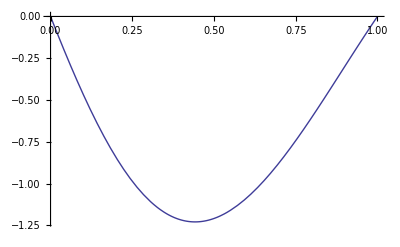

```mathematica
Plot[test21,{s,0,1}]
```

```mathematica
test22=(el1Dx1×el1Dx2).el2Dx2;
```

```mathematica
Reduce[test22==0,s,Reals]
```

s==-1.03645||s==-0.5||s==0||s==1.||s==1.95197

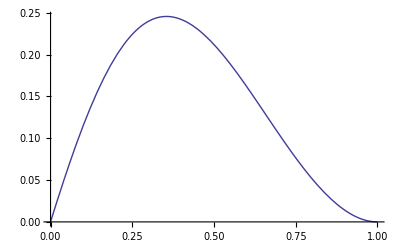

```mathematica
Plot[test22,{s,0,1}]
```

We see from the above that the tangent planes are only parallel at the nodes.
TODO: We have 2 equations, if we pick two of the degrees of freedom as unknowns, can we solve for them so as to result in tangent continuity?